```mathematica
FinancialData["NASDAQ:TSLA","Close"]
```

478.15 $

```mathematica
tsla=FinancialData["NASDAQ:TSLA","Close",All]
```

TimeSeries[…]

```mathematica
Transpose[{
tsla["Dates"][[;;-2]],
Map[#-1&,Ratios@tsla["Values"]]
}]
```

{{Tue 29 Jun 2010 00:00:00GMT-8.,-0.00251149},{Wed 30 Jun 2010 00:00:00GMT-8.,-0.0784725},{Thu 1 Jul 2010 00:00:00GMT-8.,-0.125683},2377,{Tue 7 Jan 2020 00:00:00GMT-8.,0.0492048},{Wed 8 Jan 2020 00:00:00GMT-8.,-0.021945},{Thu 9 Jan 2020 00:00:00GMT-8.,-0.00662734}}
 |  |  |  |

```mathematica
DateListPlot[
Out[3],
PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full,Joined->False
]
```

-Graphics-

```mathematica
Histogram[
Map[Last,Out[3]],
PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
```

-Graphics-

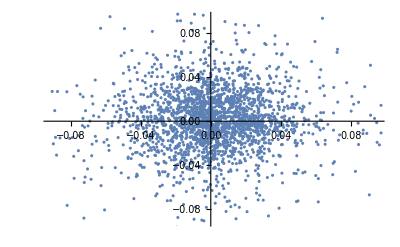

```mathematica
ListPlot[Partition[Map[Last,Out[3]],2,1]]
```

```mathematica
Histogram[
PercentForm@Map[Last,Out[3]],
PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
```

Histogram::ldata: {-0.2511%,-7.847%,-12.57%,-16.09%,-1.924%,10.51%,-0.3436%,-2.011%,6.393%,9.372%,0.252%,3.771%,6.153%,-7.348%,-0.3941%,3.858%,1.381%,-1.597%,-1.909%,0.8273%,«12»,2.511%,1.97%,-1.984%,0.1066%,1.65%,5.393%,-4.62%,3.646%,-0.7538%,-0.2532%,0.8629%,-1.963%,4.979%,2.983%,-0.04748%,-2.423%,1.753%,-0.9091%,«233300%»} is not a valid dataset or list of datasets.

General::stop: Further output of Histogram::ldata will be suppressed during this calculation.

Histogram[{-0.2511%,-7.847%,-12.57%,-16.09%,-1.924%,10.51%,-0.3436%,-2.011%,6.393%,9.372%,0.252%,3.771%,6.153%,-7.348%,-0.3941%,3.858%,1.381%,-1.597%,-1.909%,0.8273%,-1.786%,-2.015%,4.915%,4.924%,-3.144%,-3.81%,-4.205%,0.05105%,-2.908%,-5.938%,-1.676%,4.091%,2.511%,1.97%,-1.984%,0.1066%,1.65%,5.393%,-4.62%,3.646%,-0.7538%,-0.2532%,0.8629%,-1.963%,4.979%,2.983%,-0.04748%,-2.423%,1.753%,-0.9091%,-2.607%,2.727%,1.931%,4.072%,-4.732%,-3.391%,4.078%,-1.354%,-4.333%,-1.56%,2.761%,2.139%,4.238%,2.71%,-7.166%,0.9556%,1.893%,0.6193%,-3.125%,-0.1466%,0%,-0.93%,0%,1.482%,1.022%,-1.012%,-1.509%,-0.8898%,2.993%,0.4843%,-0.1446%,0.6274%,2.446%,-1.685%,0.9048%,3.067%,-1.969%,-0.7473%,2.447%,14.38%,-1.847%,2.209%,-1.401%,19.2%,-4.513%,6.438%,3.217%,-3.669%,-0.6067%,1.356%,3.68%,7.777%,3.503%,2.603%,-0.4229%,-2.803%,2.913%,-2.774%,-5.822%,-2.658%,-3.747%,4.124%,2.567%,-0.9886%,-1.654%,-3.077%,-6.612%,3.75%,4.088%,1.785%,1.084%,1.767%,1.147%,-7.784%,-15.09%,3.37%,4.998%,-4.436%,0.4906%,-0.03755%,0.1878%,0.5999%,3.914%,1.291%,0.7436%,-5.237%,-0.0000000000000111%,-2.745%,-1.793%,-0.4272%,-6.279%,-5.868%,1.857%,6.293%,0.7758%,0.2836%,0.6869%,-3.652%,0.3748%,-0.7884%,0.1255%,-1.295%,-0.7194%,-1.662%,6.155%,-5.227%,0.02155%,0.1508%,-0.7312%,-1.04%,8.275%,-4.569%,-1.78%,-5.651%,-0.1829%,3.207%,4.794%,1.186%,0.2093%,0.3342%,1.415%,2.422%,-0.04008%,-1.123%,0.2433%,-2.872%,0.2499%,-3.407%,-1.29%,-0.5665%,-0.04382%,0.6576%,-1.002%,-2.376%,0.09012%,0.5403%,1.881%,2.198%,2.882%,-0.8779%,17.04%,-3.928%,-3.113%,3.368%,-0.7865%,2.831%,-2.753%,-4.606%,-2.454%,1.136%,0.8424%,1.75%,-2.15%,0.5194%,2.345%,3.845%,-1.309%,2.046%,0.557%,2.142%,-0.2169%,-0.5435%,-2.113%,-0.6699%,-0.9367%,2.572%,2.913%,1.505%,-4.448%,2.216%,-0.4337%,-3.448%,-2.406%,1.502%,7.021%,-0.8156%,-4.112%,-0.3729%,8.458%,1.725%,0.2374%,1.997%,-5.385%,0.8521%,4.764%,-4.746%,-1.15%,-4.406%,1.844%,0.8689%,2.046%,0.598%,-4.476%,-3.001%,0%,-1.849%,5.844%,-1.162%,1.838%,-0.5233%,-0.3809%,2.367%,0.6403%,2.969%,-0.3776%,0.4135%,-0.6177%,2.659%,-3.095%,-1.597%,-0.6349%,1.668%,-3.596%,-0.1087%,-1.269%,2.424%,2.868%,0.03486%,2.056%,-2.731%,-1.72%,-1.286%,1.918%,0%,2.13%,-4.97%,-0.5121%,-9.007%,-2.061%,-2.475%,6.007%,-4.948%,6.213%,3.992%,-0.3041%,-0.4956%,-1.034%,-6.078%,-8.079%,-1.569%,4.601%,3.963%,-3.184%,2.683%,4.13%,-0.3238%,0.4466%,-2.991%,-3.875%,-0.5635%,3.923%,-0.9648%,-2.711%,-0.3918%,5.245%,1.08%,1.972%,3.948%,-0.1163%,0.9313%,-0.6151%,-0.8511%,2.926%,-3.26%,2.625%,-6.109%,-1.911%,1.119%,-2.706%,-0.295%,7.227%,6.267%,0.1113%,3.298%,-0.9684%,0.6882%,0.5036%,0.3937%,-2.246%,3.355%,-2.717%,-0.8342%,2.524%,1.855%,-1.051%,-0.9558%,2.788%,3.86%,-1.674%,-1.668%,-0.5886%,13.06%,-0.4621%,-3.219%,1.823%,-3.015%,1.457%,7.373%,-1.249%,2.137%,2.977%,-3.606%,-3.207%,-2.577%,0.9761%,-1.933%,0.6677%,2.843%,-2.488%,3.118%,-0.4276%,2.147%,3.363%,1.307%,-1.95%,-9.652%,0.4856%,-2.03%,-3.157%,-3.124%,0.3155%,-2.166%,-0.8929%,0.5405%,-1.183%,0.7254%,0.4681%,2.401%,-0.21%,0.7717%,-0.5917%,-1.681%,-1.318%,-2.129%,-0.7743%,1.263%,1.358%,2.209%,0.07085%,-19.33%,16.72%,0.7895%,-0.1865%,-0.5979%,0.6391%,2.428%,2.006%,3.468%,1.348%,0.8183%,-1.691%,1.754%,2.265%,2.975%,2.087%,-0.6289%,1.044%,2.036%,-4.543%,1.254%,5.335%,1.296%,1.726%,2.311%,-1.344%,-0.8116%,0.9059%,-2.259%,-0.3852%,0.5651%,-1.183%,2.993%,-1.075%,-0.7932%,-1.954%,0.0302%,-0.151%,5.05%,3.656%,0.2222%,-2.217%,-0.8218%,0.9143%,-0.9626%,-0.05718%,0.5435%,-2.134%,-0.9302%,9.742%,1.444%,-0.2372%,-1.374%,-0.2411%,-1.772%,3.909%,-7.919%,-1.486%,-3.857%,-2.081%,1.941%,1.058%,0.4486%,-3.989%,-0.031%,1.303%,1.531%,0%,-3.679%,-0.3757%,3.426%,1.762%,-0.4479%,-0.6299%,1.962%,0.4737%,-4.361%,-1.941%,2.011%,-7.022%,-0.4306%,9.647%,-2.154%,-6.791%,-2.096%,-0.8495%,-2.09%,-3.535%,4.39%,7.021%,0.747%,-2.257%,-1.682%,6.307%,-4.039%,-2.992%,-4.576%,-0.9591%,0.1076%,4.694%,-0.9925%,3.975%,-3.191%,1.854%,0.3709%,-1.276%,1.769%,6.453%,0.7852%,5.266%,-4.707%,4.955%,-1.998%,-3.473%,-1.721%,-0.382%,-2.844%,0.8553%,1.859%,-0.7685%,1.613%,-0.6986%,0.7675%,3.777%,4.74%,4.993%,-7.258%,-3.598%,0.3732%,-1.487%,-3.555%,-2.674%,-2.983%,-2.832%,4.906%,-7.32%,0.2559%,-4.267%,-0.5714%,4.483%,3.667%,7.004%,-3.835%,1.1%,1.802%,4.108%,-5.614%,-0.06798%,3.061%,-0.9571%,-1.666%,-1.355%,2.886%,2.604%,-4.003%,-4%,1.307%,-0.976%,0%,0.3872%,-1.332%,-0.7107%,2.183%,2.802%,-6.746%,1.571%,1.727%,4.243%,3.087%,7.075%,-3.688%,-0.9253%,-0.4831%,-2.848%,2.132%,-9.785%,-0.4338%,3.45%,2.773%,-0.4098%,2.195%,-1.678%,0.3413%,-1.735%,1.246%,-3.009%,0.1057%,-0.2817%,-2.401%,-1.122%,2.671%,2.705%,-2.703%,-1.07%,0.3965%,1.939%,-3.417%,0.3647%,-0.5087%,2.744%,3.96%,-1.119%,8.928%,-1.111%,1.252%,-0.7292%,-3.162%,2.474%,1.752%,-0.7411%,-1.785%,3.309%,3.392%,0.243%,-1.606%,-1.047%,0.4357%,-0.3719%,3.359%,1.384%,0.3859%,2.365%,-2.08%,-0.5605%,0.5636%,0.7965%,1.171%,2.054%,-0.05669%,-4.68%,0.5951%,1.745%,0.5523%,0.05782%,-0.5201%,-0.4357%,-1.721%,-1.395%,1.957%,4.399%,-1.669%,-1.064%,-0.1744%,-1.922%,-0.1188%,-0.327%,-1.849%,1.064%,1.924%,0.59%,0.8211%,0.4072%,1.941%,2.302%,2.75%,-0.02704%,2.839%,-0.2104%,-1.133%,-0.02666%,2.106%,-1.462%,1.033%,2.728%,0.7914%,-0.6079%,-2.09%,-1.379%,1.478%,-0.3901%,-3.29%,6.048%,-1.884%,-8.77%,2.702%,-4.791%,0.1454%,1.946%,-0.7692%,-0.5168%,2.684%,3.007%,2.838%,1.433%,0.6278%,1.638%,0.05115%,-0.3579%,-5.464%,-4.233%,-0.3967%,-0.1991%,2.48%,0.1669%,1.694%,2.485%,0.8793%,0.7924%,-0.7075%,15.94%,0.9333%,-7.307%,2.214%,-1.523%,1.112%,-3.18%,3.358%,4.133%,0.3671%,-1.029%,5.289%,-0.3071%,3.344%,1.831%,4.934%,1.634%,-1.137%,3.113%,-1.538%,7.305%,-1.729%,-1.315%,1.558%,0.8132%,9.074%,-6.706%,0.4981%,24.4%,10.61%,14.38%,-5.194%,1.925%,8.729%,-0.8109%,-1.705%,-2.613%,-0.3996%,6.293%,4.691%,13.65%,-5.171%,0.3068%,-6.851%,-5.288%,2.43%,0.5588%,2.076%,4.818%,-1.95%,-5.577%,3.451%,0.4604%,2.159%,1.894%,1.164%,1.248%,-3.85%,-1.093%,1.949%,0.8966%,3.242%,3.339%,-1.73%,9.146%,0.547%,-2.19%,4.209%,1.266%,1.513%,-0.9559%,2.732%,3.415%,-2.032%,-14.31%,10.27%,-1.015%,0.5461%,2.298%,0.2532%,-0.8473%,1.947%,4.288%,4.042%,-2.139%,1.928%,0.9458%,1.807%,4.841%,-1.749%,-5.572%,14.34%,-0.3127%,-3.673%,-1.323%,-4.174%,0.2224%,1.668%,2.042%,3.23%,-1.15%,6.249%,3.017%,1.471%,1.699%,-0.3353%,-0.2343%,1.77%,-0.0355%,0.9956%,-0.4056%,-1.742%,-3.755%,3.528%,-1.713%,0.8623%,0.3699%,0.6283%,-0.2101%,-0.007215%,7.04%,3.074%,-1.243%,0.6736%,1.595%,1.837%,1.198%,1.294%,-0.1913%,-6.244%,-4.222%,4.426%,1.155%,-4.556%,-3.405%,2.459%,3.337%,0.5708%,2.348%,-0.2066%,-0.4129%,0.3271%,-5.889%,-0.6141%,-4.104%,5.258%,-2.016%,-4.008%,0.9886%,-3.192%,0.4522%,1.394%,8.035%,0.919%,-14.51%,-7.534%,-1.304%,4.892%,-4.767%,0.6531%,-0.7931%,-1.563%,-10.24%,3.709%,-3.95%,0.8174%,-0.5897%,-0.4449%,-0.2814%,5.344%,0.2678%,-2.443%,16.53%,-3.974%,1.101%,-2.221%,3.087%,0.4167%,-1.786%,5.6%,0.1248%,0.1937%,3.055%,-2.938%,-4.906%,1.791%,0.2164%,5.475%,2.701%,-2.817%,0.8735%,-1.319%,-0.2187%,-0.3598%,-1.712%,1.605%,1.285%,-2.479%,-1.227%,-4.378%,15.74%,1.773%,4.167%,-0.5615%,3.923%,1.064%,1.647%,-3.802%,-2.852%,5.164%,-1.766%,4.343%,-0.7821%,-2.37%,0.9147%,-2.411%,2.27%,4.569%,5.377%,0.03052%,-0.6612%,2.207%,-0.7013%,2.759%,-4.939%,8.433%,-0.1762%,3.841%,13.94%,2.016%,-0.1818%,-3.061%,2.349%,1.708%,-0.8554%,0.1108%,-2.661%,-2.993%,-1.855%,3.02%,-1.532%,-2.868%,1.303%,2.59%,-1.75%,-0.3943%,-2.563%,-3.81%,0.1226%,-3.393%,-2.648%,2.436%,-1.846%,4.087%,6.139%,-2.123%,-5.845%,-2.217%,3.826%,0.6823%,-5.873%,-0.2008%,-2.792%,-2.11%,2.682%,-0.4972%,3.16%,6.977%,-4.871%,-0.06251%,-3.854%,-0.6705%,4.237%,0.4688%,-0.07697%,1.531%,2.703%,-4.307%,-2.861%,-11.3%,2.055%,1.322%,2.973%,0.2419%,-1.065%,1.575%,2.365%,-0.4029%,2.125%,2.722%,1.181%,2.055%,-0.6239%,0%,-1.175%,-1.478%,0.1172%,-0.4635%,1.427%,0.6143%,-1.374%,-1.466%,1.073%,-0.4646%,1.425%,8.812%,3.143%,-1.964%,0.295%,0.7902%,3.323%,-1.99%,1.889%,-0.545%,1.469%,0.4183%,-0.1416%,-4.295%,-0.07628%,-2.875%,-1.612%,1.821%,-1.614%,-0.606%,3.929%,-3.141%,-1.102%,-0.8105%,2.145%,0.2363%,-0.4353%,1.325%,0.4719%,0.01343%,0.5591%,0.08451%,1.738%,-2.455%,4.465%,2.251%,-0.01258%,4.378%,1.39%,-1.688%,4.51%,0.2468%,0.1346%,0.4111%,0.241%,-0.79%,-1.223%,-0.4089%,-0.5358%,0.9593%,2.247%,-0.3085%,0.5769%,0.2317%,2.213%,5.347%,-1.031%,1.725%,-3.024%,1.702%,-1.287%,0.9408%,-0.281%,-0.396%,-9.076%,2.71%,0.2455%,0.9335%,-1.706%,-3.582%,0.152%,0.6909%,-2.058%,-0.1417%,-0.5434%,-1.052%,-1.005%,4.654%,1.507%,2.12%,-0.4029%,-0.1117%,-0.8755%,-7.821%,-5.2%,1.1%,1.163%,-1.458%,0.4992%,1.314%,2.113%,-1.802%,1.813%,-0.02125%,-5.769%,9.519%,-1.924%,0.2352%,1.274%,0.3682%,-1.509%,-3.332%,4.438%,-0.4229%,0.7202%,3.782%,-0.7886%,1.044%,2.773%,-1.817%,1.465%,-3.865%,0.3915%,-2.384%,1.623%,0.5553%,0.1411%,-1.578%,-5.267%,-0.09066%,-0.9204%,-0.4448%,-2.002%,-4.18%,1.18%,-3.25%,-0.4575%,-0.9%,-1.43%,-3.053%,4.049%,6.044%,0.4719%,1.509%,-0.1527%,2.502%,-0.9262%,-1.542%,0.081%,-1.394%,-4.204%,0.4093%,-0.1588%,-1.878%,-2.153%,1.009%,-5.66%,-0.4256%,0.6254%,-0.5905%,2.418%,2.569%,-0.1637%,2.613%,-0.276%,-3.209%,2.924%,-0.7797%,3.605%,3.518%,0.08701%,1.116%,-1.643%,0.05521%,-0.5472%,-1.614%,-4.662%,0.4387%,0.2846%,0.05383%,3.543%,2.553%,-4.502%,-1.555%,-0.1715%,1.683%,-1.858%,-2.958%,1.133%,1.441%,-0.8916%,-3.364%,-1.547%,-0.2934%,1.797%,-1.378%,-1.251%,3.721%,-0.4957%,3.071%,-2.521%,1.242%,0.7825%,1.047%,-3.678%,-2.005%,-2.839%,3.011%,-0.9445%,-0.6251%,1.818%,6.335%,0.07385%,2.175%,1.165%,0.3855%,-0.5311%,-1.106%,0.1783%,-0.5437%,0.04354%,-0.735%,2.017%,4.79%,-0.3828%,-0.08006%,6.009%,-0.4621%,0.8547%,-2.753%,-0.008849%,1.982%,1.059%,-1.082%,2.764%,-0.08024%,1.217%,2.192%,-0.6374%,0.3783%,1.942%,-0.03617%,-0.6472%,-1.129%,0.5197%,0.8591%,-0.111%,-0.01011%,1.625%,-0.2585%,-0.5383%,-0.441%,0.2577%,-1.233%,1.309%,2.87%,-0.1132%,-2.07%,0.2832%,-0.2864%,-0.1237%,1.094%,2.88%,0.5683%,0.2367%,-1.036%,3.033%,-0.934%,1.365%,-0.6325%,-1.898%,2.382%,0.3318%,4.039%,-0.1071%,-4.233%,-4.823%,1.161%,1.644%,1.331%,-0.9448%,1.345%,2.992%,2.767%,-5.488%,0.4123%,-0.2501%,-0.6699%,-4.672%,4.668%,-0.3776%,1.126%,-0.2399%,-2.314%,2.419%,1.446%,-8.885%,-1.471%,-0.5649%,-1.563%,0.337%,1.822%,0.2639%,4.869%,2.247%,-2.098%,-5.12%,-4.711%,-5.157%,0.53%,2.186%,8.072%,2.259%,0.2334%,-4.188%,3.797%,-0.8559%,-1.482%,2.579%,0.2982%,-0.1728%,0.7083%,1.179%,0.1501%,3.423%,-0.06863%,-0.5533%,1.374%,-1.234%,0.04599%,0.7891%,-2.36%,-3.301%,-0.7165%,0.7095%,-3.43%,3.206%,-0.5736%,-1.905%,-3.934%,-2.259%,-2.66%,-2.315%,1.702%,-1.081%,2.043%,2.576%,0.4802%,-6.607%,-1.38%,0.7759%,-1.242%,2.951%,-2.281%,1.241%,-2.832%,3.315%,-2.545%,11.17%,0.06044%,0.2546%,-3.025%,-3.919%,1.192%,-2.803%,-2.7%,3.436%,-0.1446%,3.304%,0.3302%,-0.807%,-1.027%,0.2296%,5.219%,0.8579%,-0.5829%,0.7513%,0.3104%,-1.001%,0.3255%,-1.908%,-0.9704%,1.136%,-4.426%,0.7188%,1.148%,6.07%,-0.4776%,-1.255%,0.9112%,-1.122%,-0.1087%,0.3788%,-0.7026%,3.599%,0.3794%,0.8064%,-6.916%,0.008947%,-1.965%,-1.548%,-2.156%,-1.493%,1.02%,-4.601%,2.93%,-0.5772%,-0.1317%,-2.941%,0.6392%,1.29%,-3.046%,-1.436%,-2.836%,0.8667%,0.7907%,3.002%,-7.19%,-5.088%,1.066%,-7.261%,-8.825%,-3.089%,4.733%,0.3788%,2.734%,8.707%,-1.132%,-0.1139%,6.699%,-0.2982%,1.01%,4.709%,1.553%,0.8353%,-2.907%,1.068%,3.929%,2.708%,2.114%,-1.31%,3.021%,-1.696%,4.859%,1.483%,1.644%,2.005%,2.809%,2.398%,-1.712%,-4.978%,2.323%,1.102%,-0.05645%,-1.408%,1.269%,3.403%,3.956%,3.433%,3.895%,-3.097%,-2.772%,-0.05999%,-0.8403%,2.708%,-1.049%,1.052%,-0.2475%,-2.564%,1.051%,-0.6721%,2.199%,-0.7606%,0.7624%,-0.8946%,-1.495%,-2.806%,0.432%,-3.921%,-4.201%,-4.956%,1.607%,-2.796%,-0.1101%,0.1294%,-0.804%,0.1592%,0.3275%,-1.743%,3.181%,1.913%,2.356%,-1.843%,0.7816%,0.7664%,2.523%,-0.924%,0.08519%,-1.644%,-0.2733%,0.0137%,0.7717%,5.284%,1.369%,-2.615%,-4.608%,-0.4205%,-1.336%,1.275%,0.1056%,-1.129%,1.963%,-0.04096%,-10.45%,-0.1322%,-1.655%,2.796%,1.632%,4.163%,0.9943%,1.988%,-1.164%,0.215%,0.6995%,0.389%,3.69%,-0.05784%,-0.9437%,-0.4494%,-0.5101%,2.654%,-0.4376%,1.376%,-3.442%,0.8027%,3.482%,-0.2174%,-0.4444%,0.9278%,1.813%,-2.036%,-1.222%,-0.6206%,2.135%,-0.2515%,-1.682%,1.291%,-1.497%,-0.3279%,0.3112%,-0.008867%,-0.8777%,-0.1655%,0.1209%,0.6666%,-0.92%,0.8568%,-0.9874%,-0.7457%,-0.439%,-2.177%,-1.794%,0.317%,-5.302%,-1.489%,2.553%,-0.5522%,-2.157%,-1.464%,1.969%,-1.135%,0.1836%,2.042%,2.485%,0.4576%,-0.8239%,0.2834%,0.5896%,0.4941%,0.7424%,-1.522%,0.2235%,-2.7%,1.659%,4.739%,-1.072%,-1.395%,-3.579%,-2.184%,2.207%,-0.423%,0.7046%,-0.6302%,-1.863%,1.318%,2.24%,-2.191%,0.4972%,1.334%,-0.2071%,-0.04942%,0.8752%,-1.98%,-1.12%,-3.51%,-1.452%,-0.3191%,1.675%,1.391%,0.8954%,-2.503%,-2.478%,1.732%,-3.771%,1.279%,0.08706%,2.572%,-1.929%,-0.2702%,3.604%,1.03%,1.817%,-0.2695%,-3.34%,-0.08968%,-3.97%,-0.2254%,2.937%,-0.5086%,3.928%,-0.4453%,-0.05721%,0.1301%,2.973%,0.2725%,-0.5587%,2.485%,0.1185%,2.989%,-0.5221%,0.3611%,2.346%,2.901%,0.09566%,-2.303%,-0.4611%,1.544%,4.609%,-0.1057%,0.9967%,0.9912%,-0.6097%,-0.0609%,-0.06094%,3.554%,-0.9127%,1.18%,2.265%,0.3979%,1.712%,2.23%,-0.7702%,0.1743%,-0.9172%,0.5187%,-1.068%,0.9268%,-0.08746%,2.562%,-0.1125%,1.787%,2.717%,0.01114%,4.223%,0.1354%,-0.4342%,-3.864%,1.22%,1.895%,-1.399%,-6.406%,0.3945%,-2.728%,0.012%,0.184%,0.4352%,-0.1431%,-1.043%,-0.6919%,-0.798%,-0.4941%,1.018%,4.806%,-0.8798%,2.471%,-0.2099%,0.1606%,-4.291%,1.727%,-0.09019%,3.289%,2.683%,2.676%,-0.02523%,0.1947%,0.1367%,7.266%,1.735%,-2.865%,1.254%,1.286%,3.256%,-1.178%,-3.845%,2.412%,-0.8421%,-0.3948%,1.755%,0.02619%,0.7952%,0.6947%,-0.4965%,1.763%,2.789%,-1.22%,-2.468%,-5.003%,4.363%,-0.3762%,4.58%,1.233%,-0.6519%,0.5292%,-2.749%,0.3577%,-3.438%,2.27%,-0.7123%,-0.1544%,-2.091%,2.093%,2.131%,2.623%,3.063%,1.764%,-0.1877%,-0.1528%,2.198%,1.592%,1.927%,2.878%,-3.427%,0.473%,4.719%,1.253%,-1.398%,-1.05%,-0.4308%,0.6598%,1.118%,1.65%,0.2196%,-1.554%,-4.005%,2.448%,-2.826%,0.2384%,-2.486%,-7.24%,-5.583%,1.421%,0.9035%,3.534%,0.7029%,-1.854%,1.351%,-2.505%,2.713%,-0.9079%,1.433%,-0.4607%,4.3%,-0.8525%,1.251%,-2.731%,0.1824%,-3.462%,-1.206%,1.978%,6.505%,2.328%,2.83%,-0.4627%,-2.236%,0.695%,1.657%,-0.4041%,0.1601%,-3.028%,-1.267%,-2.763%,1.033%,3.346%,0.04536%,-1.383%,-0.6867%,0.4918%,1.675%,0.7701%,-0.1405%,-1.635%,-1.447%,1.765%,-2.056%,5.909%,-0.2585%,0.9593%,3.116%,0.5746%,1.366%,-2.571%,-0.3172%,-1.987%,-4.199%,-1.737%,0.07537%,-1.24%,-0.4018%,0.4417%,0.1261%,1.935%,1.973%,0.09013%,0.4362%,-3.906%,3.689%,-0.2784%,0.3046%,-0.03092%,-1.398%,1.469%,1.096%,-2.18%,-1.907%,-2.341%,0.09495%,-3.409%,0.1013%,-1.625%,-0.2462%,3.577%,-3.152%,-6.796%,2.282%,-1.081%,1.08%,-0.5424%,-0.4599%,0%,4.096%,-2.124%,0.8422%,0.3855%,0.816%,-2.003%,2.938%,-1.639%,0.9437%,0.3993%,0.2336%,-3.152%,0.426%,-0.7512%,-0.4339%,-0.4915%,3.148%,-0.6448%,1.25%,4.373%,3.685%,-0.5865%,-0.3362%,1.646%,-1.334%,-2.293%,-0.6403%,0.8146%,-1.948%,-2.432%,-1.781%,1.194%,-1.272%,2.948%,-1.023%,-0.829%,0.623%,6.264%,-0.8085%,0.3326%,0.9409%,-0.5119%,1.142%,2.088%,-0.7461%,1.582%,0.44%,0.3499%,-1.956%,-2.385%,1.543%,1.948%,-1.061%,2.455%,-1.428%,-1.575%,-3.089%,0.2522%,3.303%,-8.629%,-1.526%,1.711%,2.512%,-0.4171%,3.647%,0.4266%,-0.2146%,-0.4391%,3.861%,1.699%,1.525%,-1.799%,-2.259%,-3.536%,1.266%,-0.5282%,-1.545%,1.249%,-0.963%,-0.5864%,5.606%,-1.062%,-4.449%,-0.3153%,-1.305%,-2.424%,-0.9599%,1.926%,-2.347%,-2.446%,0.8755%,-8.219%,-7.665%,3.239%,-5.129%,5.961%,7.255%,6.545%,-2.1%,-3.221%,5.192%,-1.237%,-2.276%,2.129%,-3.04%,-1.209%,1.967%,2.294%,-3.279%,-2.367%,0.03176%,-0.9772%,1.707%,3.011%,-0.05951%,2.048%,0.4101%,-5.545%,3.389%,2.951%,-0.2642%,1.616%,-0.5964%,-1.298%,-3.019%,-2.668%,0.8094%,-0.6772%,-2.713%,2.771%,-3.332%,1.476%,-0.4372%,0.3599%,1.761%,2.805%,-2.396%,2.49%,1.686%,-1.891%,9.745%,-1.067%,0.4967%,4.546%,3.213%,0.5864%,3.753%,0.1258%,3.535%,-4.929%,2.743%,-4.061%,-3.994%,-0.1858%,2.7%,0.731%,1.576%,-1.995%,-2.298%,-7.225%,-0.5469%,-0.0841%,3.111%,1.243%,-1.088%,-0.7054%,0.682%,-2.75%,4.06%,0.3595%,-1.118%,-2.077%,-3.31%,-1.903%,3.803%,-0.6769%,-3.088%,-2.359%,2.747%,0.9056%,16.19%,-0.3919%,-1.775%,10.99%,-2.432%,-4.831%,0.8625%,0.2588%,-2.461%,-2.575%,-0.9566%,-8.928%,0.9624%,4.364%,-0.08076%,-0.4788%,0.8497%,-1.1%,-2.321%,-2.196%,-0.6098%,-0.4915%,-4.213%,-2.841%,0.07481%,-6.304%,8.456%,-2.123%,3.972%,-0.3717%,1.983%,-0.122%,-3.351%,4.934%,-0.2308%,0.2581%,0.1939%,0.4371%,2.854%,-0.6654%,-13.9%,17.35%,-3.116%,-2.066%,-4.4%,-7.054%,-4.348%,4.885%,-2.253%,-1.81%,2.597%,0.313%,6.549%,-1.739%,-2.896%,-1.482%,0.3654%,12.72%,-1.917%,9.137%,5.094%,1.194%,-1.478%,2.249%,2.063%,0.6187%,-1.446%,-0.09959%,2.082%,0.9306%,-0.2533%,-5.486%,2.249%,1.556%,1.291%,1.685%,-0.2371%,-1.692%,-2.676%,-3.655%,6.19%,-0.6012%,1.149%,-1.926%,2.729%,2.285%,0.3375%,0.9341%,-1.403%,2.007%,0.4409%,-0.04363%,2.78%,-2.941%,-4.728%,-3.269%,-1.205%,-5.283%,1.392%,-7.624%,10.39%,-3.054%,5.612%,-0.3205%,-6.815%,-3.147%,5.77%,5.436%,0.1164%,0.9483%,1.902%,0.6638%,-3.703%,2.999%,0.4703%,0.3641%,-12.97%,-1.105%,-3.79%,1.363%,1.897%,-0.2222%,0.3644%,3.802%,-0.5668%,1.69%,0.2178%,2.704%,-1.285%,-3.061%,-0.5561%,2.302%,-0.3292%,-1.167%,-1.428%,1.353%,-0.7276%,-1.008%,-3.745%,1.195%,1.378%,-0.3046%,5.667%,1.633%,-7.844%,-3.199%,-3.091%,-0.1085%,2.86%,2.386%,-2.599%,1.976%,0.3461%,-5.011%,-2.157%,-0.7496%,2.292%,0.1535%,-3.463%,-1.554%,2.822%,2.637%,1.379%,0.445%,3.33%,-1.141%,2.074%,-8.235%,2.681%,-0.6401%,-0.3258%,1.377%,-2.768%,-0.2682%,-0.4931%,2.62%,-0.7792%,0.7484%,-3.846%,0.4377%,-1.986%,-4.264%,-5.044%,2.692%,-1.151%,-1.961%,4.312%,4.478%,0.1216%,-3.243%,-0.8986%,-1.168%,-1.017%,-5.223%,2.335%,-0.155%,-1.561%,-7.577%,-2.687%,-0.1363%,-6.022%,1.432%,-2.486%,-1.012%,0.6147%,-0.8638%,-1.626%,-3.343%,8.175%,1.544%,4.761%,-0.7041%,4.098%,1.982%,-3.611%,2.222%,0.4722%,4.704%,-0.1289%,0.752%,-3.008%,1.02%,0.8023%,-1.735%,-0.223%,1.628%,0.2782%,1.66%,-1.153%,4.609%,-0.7663%,-1.184%,-0.1216%,3.851%,-0.1339%,2.716%,3.436%,-0.4418%,0.9826%,-0.5179%,1.83%,-0.9683%,1.756%,1.81%,-13.61%,-0.3409%,3.39%,2.753%,-0.2683%,-3.212%,0.2095%,-2.569%,1.064%,1.157%,2.091%,-1.381%,-2.553%,2.616%,-6.545%,-1.812%,1.994%,3.133%,-0.4276%,-2.227%,0.5977%,-4.839%,1.703%,-0.4279%,0.7053%,2.839%,1.759%,-0.2659%,-1.924%,4.033%,-0.9278%,1.908%,1.618%,4.908%,-0.4978%,-0.2725%,-0.9747%,0.8155%,-0.5311%,1.277%,-2.425%,0.2535%,-7.47%,2.46%,6.06%,-0.1773%,-0.5204%,1.586%,-0.6375%,-4.154%,-0.6866%,2.718%,0.9801%,1.866%,0.08588%,1.287%,3.659%,0.3619%,0.7212%,0.8547%,-1.916%,-1.343%,0.8205%,-0.3521%,17.67%,9.493%,-0.128%,-3.506%,-0.3826%,-0.02857%,-0.5112%,1.328%,-0.07875%,2.951%,2.744%,0.4768%,2.358%,1.403%,-1.092%,0.9361%,0.8072%,-0.619%,2.723%,-2.03%,0.741%,-6.141%,0.9909%,-2.206%,0.7205%,-0.4075%,1.494%,0.3972%,-0.9429%,-0.7987%,1.671%,1.084%,2.742%,1.107%,1.979%,-0.3586%,6.448%,-0.6579%,3.736%,2.77%,0.3836%,3.361%,1.438%,1.338%,-0.1299%,-3.643%,0.8753%,2.852%,2.963%,1.925%,3.88%,4.92%,-2.195%,-0.6627%},PlotRange→Full,PlotTheme→Marketing,ColorFunction→DarkRainbow,AspectRatio→1/3,ImageSize→Full]

```mathematica
DateListPlot[
Select[Transpose[{
tsla["Dates"][[;;-2]],
Map[#-1&,Ratios@tsla["Values"]]
}],
DateValue[First@#,"DayName"]=="Monday"&
],
PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full,Joined->False
]
```

-Graphics-

```mathematica
Select[Transpose[{
tsla["Dates"][[;;-2]],
Map[#-1&,Ratios@tsla["Values"]]
}],
DateValue[First@#,"DayName"]=="Monday"&
]
```

{}

```mathematica
Transpose[{
tsla["Dates"][[;;-2]],
Map[#-1&,Ratios@tsla["Values"]]
}]
```

{{Tue 29 Jun 2010 00:00:00GMT-8.,-0.00251149},{Wed 30 Jun 2010 00:00:00GMT-8.,-0.0784725},{Thu 1 Jul 2010 00:00:00GMT-8.,-0.125683},2377,{Tue 7 Jan 2020 00:00:00GMT-8.,0.0492048},{Wed 8 Jan 2020 00:00:00GMT-8.,-0.021945},{Thu 9 Jan 2020 00:00:00GMT-8.,-0.00662734}}
 |  |  |  |

```mathematica
DateValue[First@First@Out[12],"DayName"]
```

Tuesday

```mathematica
DateValue[First@First@Out[12],"DayName"]=="Tuesday"
```

Tuesday==Tuesday

```mathematica
Tuesday[]
```

Tuesday[]

```mathematica
DateValue[First@First@Out[12],"DayName"]==Tuesday
```

True

```mathematica
DateListPlot[
Select[Transpose[{
tsla["Dates"][[;;-2]],
Map[#-1&,Ratios@tsla["Values"]]
}],
DateValue[First@#,"DayName"]==Monday&
],
PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full,Joined->False
]
```

-Graphics-

```mathematica
GatherBy[
Transpose[{
tsla["Dates"][[;;-2]],
Map[#-1&,Ratios@tsla["Values"]]
}]
,DateValue[First@#,"DayName"]&]
```

{{{Tue 29 Jun 2010 00:00:00GMT-8.,-0.00251149},{Tue 6 Jul 2010 00:00:00GMT-8.,-0.0192427},{Tue 13 Jul 2010 00:00:00GMT-8.,0.0937156},481,{Tue 31 Dec 2019 00:00:00GMT-8.,0.0285182},{Tue 7 Jan 2020 00:00:00GMT-8.,0.0492048}},{1},{1},{1},{1}}
 |  |  |  |

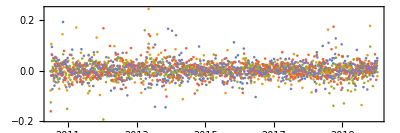

```mathematica
DateListPlot[
Out[19],
PlotRange->Full,AspectRatio->1/3,ImageSize->Full,Joined->False
]
```

```mathematica
Grid@
Table[
{f,f[Map[Last,First@Out[19]]]}
,{f,{Min,Max,Max@#-Min@#&,Mean,TrimmedMean,Quartiles,Variance,TrimmedVariance,Skewness,Kurtosis,N@Entropy@#&}}
]
```

Min | -0.145071
Max | 0.192042
Max[#1]-Min[#1]& | 0.337113
Mean | 0.00115625
TrimmedMean | 0.000792025
Quartiles | {-0.012852,0.000840071,0.0172662}
Variance | 0.000873072
TrimmedVariance | 0.000388616
Skewness | 0.462104
Kurtosis | 8.37673
N[Entropy[#1]]& | 6.18621

```mathematica
Grid@
Table[
Table[
{f,f[Map[Last,o]]}
,{f,{Min,Max,Max@#-Min@#&,Mean,TrimmedMean,Quartiles,Variance,TrimmedVariance,Skewness,Kurtosis,N@Entropy@#&}}
],
{o,Out[19]}
]
```

{Min,-0.145071} | {Max,0.192042} | {Max[#1]-Min[#1]&,0.337113} | {Mean,0.00115625} | {TrimmedMean,0.000792025} | {Quartiles,{-0.012852,0.000840071,0.0172662}} | {Variance,0.000873072} | {TrimmedVariance,0.000388616} | {Skewness,0.462104} | {Kurtosis,8.37673} | {N[Entropy[#1]]&,6.18621}
{Min,-0.136137} | {Max,0.244029} | {Max[#1]-Min[#1]&,0.380166} | {Mean,0.00196103} | {TrimmedMean,0.000728803} | {Quartiles,{-0.0142779,0.000656446,0.0172533}} | {Variance,0.00129724} | {TrimmedVariance,0.00044344} | {Skewness,1.2607} | {Kurtosis,10.9036} | {N[Entropy[#1]]&,6.19158}
{Min,-0.193274} | {Max,0.159409} | {Max[#1]-Min[#1]&,0.352683} | {Mean,-0.00102571} | {TrimmedMean,0.0000445632} | {Quartiles,{-0.0148157,0.,0.0158168}} | {Variance,0.00091565} | {TrimmedVariance,0.000340835} | {Skewness,-0.964164} | {Kurtosis,10.6936} | {N[Entropy[#1]]&,6.16125}
{Min,-0.160938} | {Max,0.173471} | {Max[#1]-Min[#1]&,0.334409} | {Mean,0.00411836} | {TrimmedMean,0.00328778} | {Quartiles,{-0.0167392,0.00225615,0.0228543}} | {Variance,0.00116016} | {TrimmedVariance,0.000551218} | {Skewness,0.5278} | {Kurtosis,6.8381} | {N[Entropy[#1]]&,6.16961}
{Min,-0.143093} | {Max,0.165338} | {Max[#1]-Min[#1]&,0.308431} | {Mean,0.00279669} | {TrimmedMean,0.00233367} | {Quartiles,{-0.0133252,0.000753673,0.0192894}} | {Variance,0.00103068} | {TrimmedVariance,0.000421962} | {Skewness,0.579277} | {Kurtosis,7.52471} | {N[Entropy[#1]]&,6.10256}

```mathematica
Grid@
Table[
Table[
{First@First@o,f,f[Map[Last,o]]}
,{f,{Min,Max,Max@#-Min@#&,Mean,TrimmedMean,Quartiles,Variance,TrimmedVariance,Skewness,Kurtosis,N@Entropy@#&}}
],
{o,Out[19]}
]
```

{Tue 29 Jun 2010 00:00:00GMT-8.,Min,-0.145071} | {Tue 29 Jun 2010 00:00:00GMT-8.,Max,0.192042} | {Tue 29 Jun 2010 00:00:00GMT-8.,Max[#1]-Min[#1]&,0.337113} | {Tue 29 Jun 2010 00:00:00GMT-8.,Mean,0.00115625} | {Tue 29 Jun 2010 00:00:00GMT-8.,TrimmedMean,0.000792025} | {Tue 29 Jun 2010 00:00:00GMT-8.,Quartiles,{-0.012852,0.000840071,0.0172662}} | {Tue 29 Jun 2010 00:00:00GMT-8.,Variance,0.000873072} | {Tue 29 Jun 2010 00:00:00GMT-8.,TrimmedVariance,0.000388616} | {Tue 29 Jun 2010 00:00:00GMT-8.,Skewness,0.462104} | {Tue 29 Jun 2010 00:00:00GMT-8.,Kurtosis,8.37673} | {Tue 29 Jun 2010 00:00:00GMT-8.,N[Entropy[#1]]&,6.18621}
{Wed 30 Jun 2010 00:00:00GMT-8.,Min,-0.136137} | {Wed 30 Jun 2010 00:00:00GMT-8.,Max,0.244029} | {Wed 30 Jun 2010 00:00:00GMT-8.,Max[#1]-Min[#1]&,0.380166} | {Wed 30 Jun 2010 00:00:00GMT-8.,Mean,0.00196103} | {Wed 30 Jun 2010 00:00:00GMT-8.,TrimmedMean,0.000728803} | {Wed 30 Jun 2010 00:00:00GMT-8.,Quartiles,{-0.0142779,0.000656446,0.0172533}} | {Wed 30 Jun 2010 00:00:00GMT-8.,Variance,0.00129724} | {Wed 30 Jun 2010 00:00:00GMT-8.,TrimmedVariance,0.00044344} | {Wed 30 Jun 2010 00:00:00GMT-8.,Skewness,1.2607} | {Wed 30 Jun 2010 00:00:00GMT-8.,Kurtosis,10.9036} | {Wed 30 Jun 2010 00:00:00GMT-8.,N[Entropy[#1]]&,6.19158}
{Thu 1 Jul 2010 00:00:00GMT-8.,Min,-0.193274} | {Thu 1 Jul 2010 00:00:00GMT-8.,Max,0.159409} | {Thu 1 Jul 2010 00:00:00GMT-8.,Max[#1]-Min[#1]&,0.352683} | {Thu 1 Jul 2010 00:00:00GMT-8.,Mean,-0.00102571} | {Thu 1 Jul 2010 00:00:00GMT-8.,TrimmedMean,0.0000445632} | {Thu 1 Jul 2010 00:00:00GMT-8.,Quartiles,{-0.0148157,0.,0.0158168}} | {Thu 1 Jul 2010 00:00:00GMT-8.,Variance,0.00091565} | {Thu 1 Jul 2010 00:00:00GMT-8.,TrimmedVariance,0.000340835} | {Thu 1 Jul 2010 00:00:00GMT-8.,Skewness,-0.964164} | {Thu 1 Jul 2010 00:00:00GMT-8.,Kurtosis,10.6936} | {Thu 1 Jul 2010 00:00:00GMT-8.,N[Entropy[#1]]&,6.16125}
{Fri 2 Jul 2010 00:00:00GMT-8.,Min,-0.160938} | {Fri 2 Jul 2010 00:00:00GMT-8.,Max,0.173471} | {Fri 2 Jul 2010 00:00:00GMT-8.,Max[#1]-Min[#1]&,0.334409} | {Fri 2 Jul 2010 00:00:00GMT-8.,Mean,0.00411836} | {Fri 2 Jul 2010 00:00:00GMT-8.,TrimmedMean,0.00328778} | {Fri 2 Jul 2010 00:00:00GMT-8.,Quartiles,{-0.0167392,0.00225615,0.0228543}} | {Fri 2 Jul 2010 00:00:00GMT-8.,Variance,0.00116016} | {Fri 2 Jul 2010 00:00:00GMT-8.,TrimmedVariance,0.000551218} | {Fri 2 Jul 2010 00:00:00GMT-8.,Skewness,0.5278} | {Fri 2 Jul 2010 00:00:00GMT-8.,Kurtosis,6.8381} | {Fri 2 Jul 2010 00:00:00GMT-8.,N[Entropy[#1]]&,6.16961}
{Mon 12 Jul 2010 00:00:00GMT-8.,Min,-0.143093} | {Mon 12 Jul 2010 00:00:00GMT-8.,Max,0.165338} | {Mon 12 Jul 2010 00:00:00GMT-8.,Max[#1]-Min[#1]&,0.308431} | {Mon 12 Jul 2010 00:00:00GMT-8.,Mean,0.00279669} | {Mon 12 Jul 2010 00:00:00GMT-8.,TrimmedMean,0.00233367} | {Mon 12 Jul 2010 00:00:00GMT-8.,Quartiles,{-0.0133252,0.000753673,0.0192894}} | {Mon 12 Jul 2010 00:00:00GMT-8.,Variance,0.00103068} | {Mon 12 Jul 2010 00:00:00GMT-8.,TrimmedVariance,0.000421962} | {Mon 12 Jul 2010 00:00:00GMT-8.,Skewness,0.579277} | {Mon 12 Jul 2010 00:00:00GMT-8.,Kurtosis,7.52471} | {Mon 12 Jul 2010 00:00:00GMT-8.,N[Entropy[#1]]&,6.10256}

```mathematica
Table[
Table[
{First@First@o,f,f[Map[Last,o]]}
,{f,{Min,Max,Max@#-Min@#&,Mean,TrimmedMean,Quartiles,Variance,TrimmedVariance,Skewness,Kurtosis,N@Entropy@#&}}
],
{o,Out[19]}
]
```

{{{Tue 29 Jun 2010 00:00:00GMT-8.,Min,-0.145071},{Tue 29 Jun 2010 00:00:00GMT-8.,Max,0.192042},{Tue 29 Jun 2010 00:00:00GMT-8.,Max[#1]-Min[#1]&,0.337113},{Tue 29 Jun 2010 00:00:00GMT-8.,Mean,0.00115625},{Tue 29 Jun 2010 00:00:00GMT-8.,TrimmedMean,0.000792025},{Tue 29 Jun 2010 00:00:00GMT-8.,Quartiles,{-0.012852,0.000840071,0.0172662}},{Tue 29 Jun 2010 00:00:00GMT-8.,Variance,0.000873072},{Tue 29 Jun 2010 00:00:00GMT-8.,TrimmedVariance,0.000388616},{Tue 29 Jun 2010 00:00:00GMT-8.,Skewness,0.462104},{Tue 29 Jun 2010 00:00:00GMT-8.,Kurtosis,8.37673},{Tue 29 Jun 2010 00:00:00GMT-8.,N[Entropy[#1]]&,6.18621}},{{Wed 30 Jun 2010 00:00:00GMT-8.,Min,-0.136137},{Wed 30 Jun 2010 00:00:00GMT-8.,Max,0.244029},{Wed 30 Jun 2010 00:00:00GMT-8.,Max[#1]-Min[#1]&,0.380166},{Wed 30 Jun 2010 00:00:00GMT-8.,Mean,0.00196103},{Wed 30 Jun 2010 00:00:00GMT-8.,TrimmedMean,0.000728803},{Wed 30 Jun 2010 00:00:00GMT-8.,Quartiles,{-0.0142779,0.000656446,0.0172533}},{Wed 30 Jun 2010 00:00:00GMT-8.,Variance,0.00129724},{Wed 30 Jun 2010 00:00:00GMT-8.,TrimmedVariance,0.00044344},{Wed 30 Jun 2010 00:00:00GMT-8.,Skewness,1.2607},{Wed 30 Jun 2010 00:00:00GMT-8.,Kurtosis,10.9036},{Wed 30 Jun 2010 00:00:00GMT-8.,N[Entropy[#1]]&,6.19158}},{{Thu 1 Jul 2010 00:00:00GMT-8.,Min,-0.193274},{Thu 1 Jul 2010 00:00:00GMT-8.,Max,0.159409},{Thu 1 Jul 2010 00:00:00GMT-8.,Max[#1]-Min[#1]&,0.352683},{Thu 1 Jul 2010 00:00:00GMT-8.,Mean,-0.00102571},{Thu 1 Jul 2010 00:00:00GMT-8.,TrimmedMean,0.0000445632},{Thu 1 Jul 2010 00:00:00GMT-8.,Quartiles,{-0.0148157,0.,0.0158168}},{Thu 1 Jul 2010 00:00:00GMT-8.,Variance,0.00091565},{Thu 1 Jul 2010 00:00:00GMT-8.,TrimmedVariance,0.000340835},{Thu 1 Jul 2010 00:00:00GMT-8.,Skewness,-0.964164},{Thu 1 Jul 2010 00:00:00GMT-8.,Kurtosis,10.6936},{Thu 1 Jul 2010 00:00:00GMT-8.,N[Entropy[#1]]&,6.16125}},{{Fri 2 Jul 2010 00:00:00GMT-8.,Min,-0.160938},{Fri 2 Jul 2010 00:00:00GMT-8.,Max,0.173471},{Fri 2 Jul 2010 00:00:00GMT-8.,Max[#1]-Min[#1]&,0.334409},{Fri 2 Jul 2010 00:00:00GMT-8.,Mean,0.00411836},{Fri 2 Jul 2010 00:00:00GMT-8.,TrimmedMean,0.00328778},{Fri 2 Jul 2010 00:00:00GMT-8.,Quartiles,{-0.0167392,0.00225615,0.0228543}},{Fri 2 Jul 2010 00:00:00GMT-8.,Variance,0.00116016},{Fri 2 Jul 2010 00:00:00GMT-8.,TrimmedVariance,0.000551218},{Fri 2 Jul 2010 00:00:00GMT-8.,Skewness,0.5278},{Fri 2 Jul 2010 00:00:00GMT-8.,Kurtosis,6.8381},{Fri 2 Jul 2010 00:00:00GMT-8.,N[Entropy[#1]]&,6.16961}},{{Mon 12 Jul 2010 00:00:00GMT-8.,Min,-0.143093},{Mon 12 Jul 2010 00:00:00GMT-8.,Max,0.165338},{Mon 12 Jul 2010 00:00:00GMT-8.,Max[#1]-Min[#1]&,0.308431},{Mon 12 Jul 2010 00:00:00GMT-8.,Mean,0.00279669},{Mon 12 Jul 2010 00:00:00GMT-8.,TrimmedMean,0.00233367},{Mon 12 Jul 2010 00:00:00GMT-8.,Quartiles,{-0.0133252,0.000753673,0.0192894}},{Mon 12 Jul 2010 00:00:00GMT-8.,Variance,0.00103068},{Mon 12 Jul 2010 00:00:00GMT-8.,TrimmedVariance,0.000421962},{Mon 12 Jul 2010 00:00:00GMT-8.,Skewness,0.579277},{Mon 12 Jul 2010 00:00:00GMT-8.,Kurtosis,7.52471},{Mon 12 Jul 2010 00:00:00GMT-8.,N[Entropy[#1]]&,6.10256}}}

```mathematica
Flatten[
Table[
Table[
{First@First@o,f,f[Map[Last,o]]}
,{f,{Min,Max,Max@#-Min@#&,Mean,TrimmedMean,Quartiles,Variance,TrimmedVariance,Skewness,Kurtosis,N@Entropy@#&}}
],
{o,Out[19]}
]
,1]
```

{{Tue 29 Jun 2010 00:00:00GMT-8.,Min,-0.145071},{Tue 29 Jun 2010 00:00:00GMT-8.,Max,0.192042},{Tue 29 Jun 2010 00:00:00GMT-8.,Max[#1]-Min[#1]&,0.337113},{Tue 29 Jun 2010 00:00:00GMT-8.,Mean,0.00115625},{Tue 29 Jun 2010 00:00:00GMT-8.,TrimmedMean,0.000792025},{Tue 29 Jun 2010 00:00:00GMT-8.,Quartiles,{-0.012852,0.000840071,0.0172662}},{Tue 29 Jun 2010 00:00:00GMT-8.,Variance,0.000873072},{Tue 29 Jun 2010 00:00:00GMT-8.,TrimmedVariance,0.000388616},{Tue 29 Jun 2010 00:00:00GMT-8.,Skewness,0.462104},{Tue 29 Jun 2010 00:00:00GMT-8.,Kurtosis,8.37673},{Tue 29 Jun 2010 00:00:00GMT-8.,N[Entropy[#1]]&,6.18621},{Wed 30 Jun 2010 00:00:00GMT-8.,Min,-0.136137},{Wed 30 Jun 2010 00:00:00GMT-8.,Max,0.244029},{Wed 30 Jun 2010 00:00:00GMT-8.,Max[#1]-Min[#1]&,0.380166},{Wed 30 Jun 2010 00:00:00GMT-8.,Mean,0.00196103},{Wed 30 Jun 2010 00:00:00GMT-8.,TrimmedMean,0.000728803},{Wed 30 Jun 2010 00:00:00GMT-8.,Quartiles,{-0.0142779,0.000656446,0.0172533}},{Wed 30 Jun 2010 00:00:00GMT-8.,Variance,0.00129724},{Wed 30 Jun 2010 00:00:00GMT-8.,TrimmedVariance,0.00044344},{Wed 30 Jun 2010 00:00:00GMT-8.,Skewness,1.2607},{Wed 30 Jun 2010 00:00:00GMT-8.,Kurtosis,10.9036},{Wed 30 Jun 2010 00:00:00GMT-8.,N[Entropy[#1]]&,6.19158},{Thu 1 Jul 2010 00:00:00GMT-8.,Min,-0.193274},{Thu 1 Jul 2010 00:00:00GMT-8.,Max,0.159409},{Thu 1 Jul 2010 00:00:00GMT-8.,Max[#1]-Min[#1]&,0.352683},{Thu 1 Jul 2010 00:00:00GMT-8.,Mean,-0.00102571},{Thu 1 Jul 2010 00:00:00GMT-8.,TrimmedMean,0.0000445632},{Thu 1 Jul 2010 00:00:00GMT-8.,Quartiles,{-0.0148157,0.,0.0158168}},{Thu 1 Jul 2010 00:00:00GMT-8.,Variance,0.00091565},{Thu 1 Jul 2010 00:00:00GMT-8.,TrimmedVariance,0.000340835},{Thu 1 Jul 2010 00:00:00GMT-8.,Skewness,-0.964164},{Thu 1 Jul 2010 00:00:00GMT-8.,Kurtosis,10.6936},{Thu 1 Jul 2010 00:00:00GMT-8.,N[Entropy[#1]]&,6.16125},{Fri 2 Jul 2010 00:00:00GMT-8.,Min,-0.160938},{Fri 2 Jul 2010 00:00:00GMT-8.,Max,0.173471},{Fri 2 Jul 2010 00:00:00GMT-8.,Max[#1]-Min[#1]&,0.334409},{Fri 2 Jul 2010 00:00:00GMT-8.,Mean,0.00411836},{Fri 2 Jul 2010 00:00:00GMT-8.,TrimmedMean,0.00328778},{Fri 2 Jul 2010 00:00:00GMT-8.,Quartiles,{-0.0167392,0.00225615,0.0228543}},{Fri 2 Jul 2010 00:00:00GMT-8.,Variance,0.00116016},{Fri 2 Jul 2010 00:00:00GMT-8.,TrimmedVariance,0.000551218},{Fri 2 Jul 2010 00:00:00GMT-8.,Skewness,0.5278},{Fri 2 Jul 2010 00:00:00GMT-8.,Kurtosis,6.8381},{Fri 2 Jul 2010 00:00:00GMT-8.,N[Entropy[#1]]&,6.16961},{Mon 12 Jul 2010 00:00:00GMT-8.,Min,-0.143093},{Mon 12 Jul 2010 00:00:00GMT-8.,Max,0.165338},{Mon 12 Jul 2010 00:00:00GMT-8.,Max[#1]-Min[#1]&,0.308431},{Mon 12 Jul 2010 00:00:00GMT-8.,Mean,0.00279669},{Mon 12 Jul 2010 00:00:00GMT-8.,TrimmedMean,0.00233367},{Mon 12 Jul 2010 00:00:00GMT-8.,Quartiles,{-0.0133252,0.000753673,0.0192894}},{Mon 12 Jul 2010 00:00:00GMT-8.,Variance,0.00103068},{Mon 12 Jul 2010 00:00:00GMT-8.,TrimmedVariance,0.000421962},{Mon 12 Jul 2010 00:00:00GMT-8.,Skewness,0.579277},{Mon 12 Jul 2010 00:00:00GMT-8.,Kurtosis,7.52471},{Mon 12 Jul 2010 00:00:00GMT-8.,N[Entropy[#1]]&,6.10256}}

```mathematica
Grid@
Flatten[
Table[
Table[
{First@First@o,f,f[Map[Last,o]]}
,{f,{Min,Max,Max@#-Min@#&,Mean,TrimmedMean,Quartiles,Variance,TrimmedVariance,Skewness,Kurtosis,N@Entropy@#&}}
],
{o,Out[19]}
]
,1]
```

Tue 29 Jun 2010 00:00:00GMT-8. | Min | -0.145071
Tue 29 Jun 2010 00:00:00GMT-8. | Max | 0.192042
Tue 29 Jun 2010 00:00:00GMT-8. | Max[#1]-Min[#1]& | 0.337113
Tue 29 Jun 2010 00:00:00GMT-8. | Mean | 0.00115625
Tue 29 Jun 2010 00:00:00GMT-8. | TrimmedMean | 0.000792025
Tue 29 Jun 2010 00:00:00GMT-8. | Quartiles | {-0.012852,0.000840071,0.0172662}
Tue 29 Jun 2010 00:00:00GMT-8. | Variance | 0.000873072
Tue 29 Jun 2010 00:00:00GMT-8. | TrimmedVariance | 0.000388616
Tue 29 Jun 2010 00:00:00GMT-8. | Skewness | 0.462104
Tue 29 Jun 2010 00:00:00GMT-8. | Kurtosis | 8.37673
Tue 29 Jun 2010 00:00:00GMT-8. | N[Entropy[#1]]& | 6.18621
Wed 30 Jun 2010 00:00:00GMT-8. | Min | -0.136137
Wed 30 Jun 2010 00:00:00GMT-8. | Max | 0.244029
Wed 30 Jun 2010 00:00:00GMT-8. | Max[#1]-Min[#1]& | 0.380166
Wed 30 Jun 2010 00:00:00GMT-8. | Mean | 0.00196103
Wed 30 Jun 2010 00:00:00GMT-8. | TrimmedMean | 0.000728803
Wed 30 Jun 2010 00:00:00GMT-8. | Quartiles | {-0.0142779,0.000656446,0.0172533}
Wed 30 Jun 2010 00:00:00GMT-8. | Variance | 0.00129724
Wed 30 Jun 2010 00:00:00GMT-8. | TrimmedVariance | 0.00044344
Wed 30 Jun 2010 00:00:00GMT-8. | Skewness | 1.2607
Wed 30 Jun 2010 00:00:00GMT-8. | Kurtosis | 10.9036
Wed 30 Jun 2010 00:00:00GMT-8. | N[Entropy[#1]]& | 6.19158
Thu 1 Jul 2010 00:00:00GMT-8. | Min | -0.193274
Thu 1 Jul 2010 00:00:00GMT-8. | Max | 0.159409
Thu 1 Jul 2010 00:00:00GMT-8. | Max[#1]-Min[#1]& | 0.352683
Thu 1 Jul 2010 00:00:00GMT-8. | Mean | -0.00102571
Thu 1 Jul 2010 00:00:00GMT-8. | TrimmedMean | 0.0000445632
Thu 1 Jul 2010 00:00:00GMT-8. | Quartiles | {-0.0148157,0.,0.0158168}
Thu 1 Jul 2010 00:00:00GMT-8. | Variance | 0.00091565
Thu 1 Jul 2010 00:00:00GMT-8. | TrimmedVariance | 0.000340835
Thu 1 Jul 2010 00:00:00GMT-8. | Skewness | -0.964164
Thu 1 Jul 2010 00:00:00GMT-8. | Kurtosis | 10.6936
Thu 1 Jul 2010 00:00:00GMT-8. | N[Entropy[#1]]& | 6.16125
Fri 2 Jul 2010 00:00:00GMT-8. | Min | -0.160938
Fri 2 Jul 2010 00:00:00GMT-8. | Max | 0.173471
Fri 2 Jul 2010 00:00:00GMT-8. | Max[#1]-Min[#1]& | 0.334409
Fri 2 Jul 2010 00:00:00GMT-8. | Mean | 0.00411836
Fri 2 Jul 2010 00:00:00GMT-8. | TrimmedMean | 0.00328778
Fri 2 Jul 2010 00:00:00GMT-8. | Quartiles | {-0.0167392,0.00225615,0.0228543}
Fri 2 Jul 2010 00:00:00GMT-8. | Variance | 0.00116016
Fri 2 Jul 2010 00:00:00GMT-8. | TrimmedVariance | 0.000551218
Fri 2 Jul 2010 00:00:00GMT-8. | Skewness | 0.5278
Fri 2 Jul 2010 00:00:00GMT-8. | Kurtosis | 6.8381
Fri 2 Jul 2010 00:00:00GMT-8. | N[Entropy[#1]]& | 6.16961
Mon 12 Jul 2010 00:00:00GMT-8. | Min | -0.143093
Mon 12 Jul 2010 00:00:00GMT-8. | Max | 0.165338
Mon 12 Jul 2010 00:00:00GMT-8. | Max[#1]-Min[#1]& | 0.308431
Mon 12 Jul 2010 00:00:00GMT-8. | Mean | 0.00279669
Mon 12 Jul 2010 00:00:00GMT-8. | TrimmedMean | 0.00233367
Mon 12 Jul 2010 00:00:00GMT-8. | Quartiles | {-0.0133252,0.000753673,0.0192894}
Mon 12 Jul 2010 00:00:00GMT-8. | Variance | 0.00103068
Mon 12 Jul 2010 00:00:00GMT-8. | TrimmedVariance | 0.000421962
Mon 12 Jul 2010 00:00:00GMT-8. | Skewness | 0.579277
Mon 12 Jul 2010 00:00:00GMT-8. | Kurtosis | 7.52471
Mon 12 Jul 2010 00:00:00GMT-8. | N[Entropy[#1]]& | 6.10256

```mathematica
Grid@
Flatten[
Table[
Table[
{DateValue[First@First@o,"DayName"],f,f[Map[Last,o]]}
,{f,{Min,Max,Max@#-Min@#&,Mean,TrimmedMean,Quartiles,Variance,TrimmedVariance,Skewness,Kurtosis,N@Entropy@#&}}
],
{o,Out[19]}
]
,1]
```

Tuesday | Min | -0.145071
Tuesday | Max | 0.192042
Tuesday | Max[#1]-Min[#1]& | 0.337113
Tuesday | Mean | 0.00115625
Tuesday | TrimmedMean | 0.000792025
Tuesday | Quartiles | {-0.012852,0.000840071,0.0172662}
Tuesday | Variance | 0.000873072
Tuesday | TrimmedVariance | 0.000388616
Tuesday | Skewness | 0.462104
Tuesday | Kurtosis | 8.37673
Tuesday | N[Entropy[#1]]& | 6.18621
Wednesday | Min | -0.136137
Wednesday | Max | 0.244029
Wednesday | Max[#1]-Min[#1]& | 0.380166
Wednesday | Mean | 0.00196103
Wednesday | TrimmedMean | 0.000728803
Wednesday | Quartiles | {-0.0142779,0.000656446,0.0172533}
Wednesday | Variance | 0.00129724
Wednesday | TrimmedVariance | 0.00044344
Wednesday | Skewness | 1.2607
Wednesday | Kurtosis | 10.9036
Wednesday | N[Entropy[#1]]& | 6.19158
Thursday | Min | -0.193274
Thursday | Max | 0.159409
Thursday | Max[#1]-Min[#1]& | 0.352683
Thursday | Mean | -0.00102571
Thursday | TrimmedMean | 0.0000445632
Thursday | Quartiles | {-0.0148157,0.,0.0158168}
Thursday | Variance | 0.00091565
Thursday | TrimmedVariance | 0.000340835
Thursday | Skewness | -0.964164
Thursday | Kurtosis | 10.6936
Thursday | N[Entropy[#1]]& | 6.16125
Friday | Min | -0.160938
Friday | Max | 0.173471
Friday | Max[#1]-Min[#1]& | 0.334409
Friday | Mean | 0.00411836
Friday | TrimmedMean | 0.00328778
Friday | Quartiles | {-0.0167392,0.00225615,0.0228543}
Friday | Variance | 0.00116016
Friday | TrimmedVariance | 0.000551218
Friday | Skewness | 0.5278
Friday | Kurtosis | 6.8381
Friday | N[Entropy[#1]]& | 6.16961
Monday | Min | -0.143093
Monday | Max | 0.165338
Monday | Max[#1]-Min[#1]& | 0.308431
Monday | Mean | 0.00279669
Monday | TrimmedMean | 0.00233367
Monday | Quartiles | {-0.0133252,0.000753673,0.0192894}
Monday | Variance | 0.00103068
Monday | TrimmedVariance | 0.000421962
Monday | Skewness | 0.579277
Monday | Kurtosis | 7.52471
Monday | N[Entropy[#1]]& | 6.10256

```mathematica
Grid@
Flatten[
Table[
Table[
{DateValue[First@First@o,"DayName"],f,f[Map[Last,o]]}
,{f,{Min,Max,Max@#-Min@#&,Mean,TrimmedMean,GeometricMean,Quartiles,Variance,TrimmedVariance,Skewness,Kurtosis,N@Entropy@#&}}
],
{o,Out[19]}
]
,1]
```

Tuesday | Min | -0.145071
Tuesday | Max | 0.192042
Tuesday | Max[#1]-Min[#1]& | 0.337113
Tuesday | Mean | 0.00115625
Tuesday | TrimmedMean | 0.000792025
Tuesday | GeometricMean | 0.0117322+0.00007584 ⅈ
Tuesday | Quartiles | {-0.012852,0.000840071,0.0172662}
Tuesday | Variance | 0.000873072
Tuesday | TrimmedVariance | 0.000388616
Tuesday | Skewness | 0.462104
Tuesday | Kurtosis | 8.37673
Tuesday | N[Entropy[#1]]& | 6.18621
Wednesday | Min | -0.136137
Wednesday | Max | 0.244029
Wednesday | Max[#1]-Min[#1]& | 0.380166
Wednesday | Mean | 0.00196103
Wednesday | TrimmedMean | 0.000728803
Wednesday | GeometricMean | 0.
Wednesday | Quartiles | {-0.0142779,0.000656446,0.0172533}
Wednesday | Variance | 0.00129724
Wednesday | TrimmedVariance | 0.00044344
Wednesday | Skewness | 1.2607
Wednesday | Kurtosis | 10.9036
Wednesday | N[Entropy[#1]]& | 6.19158
Thursday | Min | -0.193274
Thursday | Max | 0.159409
Thursday | Max[#1]-Min[#1]& | 0.352683
Thursday | Mean | -0.00102571
Thursday | TrimmedMean | 0.0000445632
Thursday | GeometricMean | 0.
Thursday | Quartiles | {-0.0148157,0.,0.0158168}
Thursday | Variance | 0.00091565
Thursday | TrimmedVariance | 0.000340835
Thursday | Skewness | -0.964164
Thursday | Kurtosis | 10.6936
Thursday | N[Entropy[#1]]& | 6.16125
Friday | Min | -0.160938
Friday | Max | 0.173471
Friday | Max[#1]-Min[#1]& | 0.334409
Friday | Mean | 0.00411836
Friday | TrimmedMean | 0.00328778
Friday | GeometricMean | 0.0158657+0.000104277 ⅈ
Friday | Quartiles | {-0.0167392,0.00225615,0.0228543}
Friday | Variance | 0.00116016
Friday | TrimmedVariance | 0.000551218
Friday | Skewness | 0.5278
Friday | Kurtosis | 6.8381
Friday | N[Entropy[#1]]& | 6.16961
Monday | Min | -0.143093
Monday | Max | 0.165338
Monday | Max[#1]-Min[#1]& | 0.308431
Monday | Mean | 0.00279669
Monday | TrimmedMean | 0.00233367
Monday | GeometricMean | 0.
Monday | Quartiles | {-0.0133252,0.000753673,0.0192894}
Monday | Variance | 0.00103068
Monday | TrimmedVariance | 0.000421962
Monday | Skewness | 0.579277
Monday | Kurtosis | 7.52471
Monday | N[Entropy[#1]]& | 6.10256

```mathematica
Grid@
Table[
{DateValue[First@First@o,"DayName"],Mean[Map[Last,o]]}
,{o,Out[19]}
]
```

Tuesday | 0.00115625
Wednesday | 0.00196103
Thursday | -0.00102571
Friday | 0.00411836
Monday | 0.00279669

```mathematica
With[{f=Mean},
Grid@
ReverseSortBy[
Table[
{DateValue[First@First@o,"DayName"],f[Map[Last,o]]}
,{o,Out[19]}
]
,Last]
]
```

Friday | 0.00411836
Monday | 0.00279669
Wednesday | 0.00196103
Tuesday | 0.00115625
Thursday | -0.00102571

```mathematica
With[{f=Variance},
Grid@
ReverseSortBy[
Table[
{DateValue[First@First@o,"DayName"],f[Map[Last,o]]}
,{o,Out[19]}
]
,Last]
]
```

Wednesday | 0.00129724
Friday | 0.00116016
Monday | 0.00103068
Thursday | 0.00091565
Tuesday | 0.000873072

```mathematica
With[{f=Quartiles},
Grid@
ReverseSortBy[
Table[
{DateValue[First@First@o,"DayName"],f[Map[Last,o]]}
,{o,Out[19]}
]
,Last]
]
```

Tuesday | {-0.012852,0.000840071,0.0172662}
Monday | {-0.0133252,0.000753673,0.0192894}
Wednesday | {-0.0142779,0.000656446,0.0172533}
Thursday | {-0.0148157,0.,0.0158168}
Friday | {-0.0167392,0.00225615,0.0228543}

```mathematica
With[{f=Skewness},
Grid@
ReverseSortBy[
Table[
{DateValue[First@First@o,"DayName"],f[Map[Last,o]]}
,{o,Out[19]}
]
,Last]
]
```

Wednesday | 1.2607
Monday | 0.579277
Friday | 0.5278
Tuesday | 0.462104
Thursday | -0.964164

```mathematica
With[{f=Kurtosis},
Grid@
ReverseSortBy[
Table[
{DateValue[First@First@o,"DayName"],f[Map[Last,o]]}
,{o,Out[19]}
]
,Last]
]
```

Wednesday | 10.9036
Thursday | 10.6936
Tuesday | 8.37673
Monday | 7.52471
Friday | 6.8381

```mathematica
With[{f=Kurtosis},
Grid@
Table[
{DateValue[First@First@o,"DayName"],Histogram[
Map[Last,o],
PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]}
,{o,Out[19]}
]
]
```

Tuesday | -Graphics-
Wednesday | -Graphics-
Thursday | -Graphics-
Friday | -Graphics-
Monday | -Graphics-

```mathematica
With[{f=Kurtosis},
Grid@
Table[
{DateValue[First@First@o,"DayName"],Histogram[
Map[Last,o],
PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Medium
]}
,{o,Out[19]}
]
]
```

Tuesday | -Graphics-
Wednesday | -Graphics-
Thursday | -Graphics-
Friday | -Graphics-
Monday | -Graphics-

```mathematica
With[{stock=FinancialData["NASDAQ:AAPL","Close",All]},
With[{
days=GatherBy[
Transpose[{
stock["Dates"][[;;-2]],
Map[#-1&,Ratios@stock["Values"]]
}]
,DateValue[First@#,"DayName"]&]},
Grid@
Table[
{DateValue[First@First@o,"DayName"],Histogram[
Map[Last,o],
PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Medium
]}
,{o,days}
]
]
]
```

Friday | -Graphics-
Monday | -Graphics-
Tuesday | -Graphics-
Wednesday | -Graphics-
Thursday | -Graphics-

```mathematica
With[{f=Kurtosis,stock=FinancialData["NASDAQ:AAPL","Close",All]},
With[{
days=GatherBy[
Transpose[{
stock["Dates"][[;;-2]],
Map[#-1&,Ratios@stock["Values"]]
}]
,DateValue[First@#,"DayName"]&]},
Grid@
ReverseSortBy[
Table[
{DateValue[First@First@o,"DayName"],f[Map[Last,o]]}
,{o,Out[19]}
]
,Last]
]
]
```

Wednesday | 10.9036
Thursday | 10.6936
Tuesday | 8.37673
Monday | 7.52471
Friday | 6.8381

```mathematica
With[{f=Kurtosis},
Grid@
ReverseSortBy[
Table[
{DateValue[First@First@o,"DayName"],f[Map[Last,o]]}
,{o,Out[19]}
]
,Last]
]
```

```mathematica
With[{f=Mean,stock=FinancialData["NASDAQ:AAPL","Close",All]},
With[{
days=GatherBy[
Transpose[{
stock["Dates"][[;;-2]],
Map[#-1&,Ratios@stock["Values"]]
}]
,DateValue[First@#,"DayName"]&]},
Grid@
ReverseSortBy[
Table[
{DateValue[First@First@o,"DayName"],f[Map[Last,o]]}
,{o,Out[19]}
]
,Last]
]
]
```

Friday | 0.00411836
Monday | 0.00279669
Wednesday | 0.00196103
Tuesday | 0.00115625
Thursday | -0.00102571

```mathematica
With[{f=Variance,stock=FinancialData["NASDAQ:AAPL","Close",All]},
With[{
days=GatherBy[
Transpose[{
stock["Dates"][[;;-2]],
Map[#-1&,Ratios@stock["Values"]]
}]
,DateValue[First@#,"DayName"]&]},
Grid@
ReverseSortBy[
Table[
{DateValue[First@First@o,"DayName"],f[Map[Last,o]]}
,{o,Out[19]}
]
,Last]
]
]
```

Wednesday | 0.00129724
Friday | 0.00116016
Monday | 0.00103068
Thursday | 0.00091565
Tuesday | 0.000873072

```mathematica
With[{f=Median,stock=FinancialData["NASDAQ:AAPL","Close",All]},
With[{
days=GatherBy[
Transpose[{
stock["Dates"][[;;-2]],
Map[#-1&,Ratios@stock["Values"]]
}]
,DateValue[First@#,"DayName"]&]},
Grid@
ReverseSortBy[
Table[
{DateValue[First@First@o,"DayName"],f[Map[Last,o]]}
,{o,Out[19]}
]
,Last]
]
]
```

Friday | 0.00225615
Tuesday | 0.000840071
Monday | 0.000753673
Wednesday | 0.000656446
Thursday | 0.

```mathematica
With[{stock=FinancialData["^SPX","Close",All]},
With[{
days=GatherBy[
Transpose[{
stock["Dates"][[;;-2]],
Map[#-1&,Ratios@stock["Values"]]
}]
,DateValue[First@#,"DayName"]&]},
Grid@
Table[
{DateValue[First@First@o,"DayName"],Histogram[
Map[Last,o],
PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Medium
]}
,{o,days}
]
]
]
```

Tuesday | -Graphics-
Wednesday | -Graphics-
Thursday | -Graphics-
Friday | -Graphics-
Monday | -Graphics-